The two parameters that tune temperature are particle density, n, and ΔE:

n = 6.67/9 T;   ΔE=1-E_min=8.33*10^-4 T

By fitting to data generated by a simulation of electron flow through a constriction, Arthur found

l_ee=7.5/(n(ΔE)^0.8)

where l_ee is the mean free path of electrons between collisions with other electrons. We may assert that its temperature dependence takes the form:

l_ee=α/T^p

where p < 2. It follows that temperature, if the particle density is held fixed, is related to ΔE by

ΔE^0.8 = (7.5 T^p)/(α n)

To determine α, I fit the following mean free path length data with a T^-p dependent function

```mathematica
ClearAll["Global`*"]
scatteringLengthVsTemp = {{31,4.13},{37,3.22},{40.5,2.65},{46,2.19},{51,1.9},{54.5,1.64},{60,1.4},{63.5,1.25},{69,1.15},
{72,1.07},{80,0.96},{85,0.90},{90,0.82},{95,0.79},{100,0.75},{105,0.7},{110,0.67},{115,0.65},{120,0.6},{125,0.58},
{130,0.55},{135,0.53},{140,.51},{145,0.49},{150,0.47},{155,0.45},{160,0.43},{165,0.42},{170,0.41},{175,0.4},{180,0.39},
{185,0.37},{190,0.36},{195,0.35},{200,0.33},{205,0.32},{210,0.31},{215,0.30},{220,0.29},{225,0.28},{230,0.27},{235,0.26},
{240,0.25},{245,0.24},{250,0.23}};
```

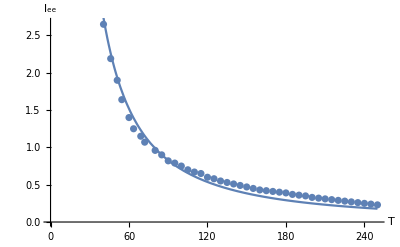

lee (in Microns) = 705.281/T^1.5

```mathematica
p = 1.5;
lee[T_]:=Fit[scatteringLengthVsTemp, {x^(- p)}, x]/.x->T 
(* fit data with 1/T^-p dependence *)
Show[ ListPlot[scatteringLengthVsTemp], Plot[ {lee[T]}, {T, 0, 250}], AxesLabel->{"T", "l_ee"}]
StringForm["lee (in Microns) = ``", lee[T]]
```

Therefore I find that

```mathematica
Emin[T_, n_]:= 1- ((7.5 T^p)/(α n))^(1/0.8)/. α-> 705.3
StringForm["E_min = ``", Emin[T,n]//FullSimplify]
Plot3D[ {0.8, Emin[T,n]}, {T, 0, 300}, {n, 0, 500}, PlotRange->{0,1}, AxesLabel->Automatic]
```

E_min = 1-0.00341475 (T^1.5/n)^1.25

-Graphics3D-

For all Simulations, we want to keep E_min > 0.8. For any given temperature we wish to simulate, choose n such that the we are in the region above the E_min=0.8 plane in this plot.